## Figure 2.3c

```mathematica
(*Loading the melt package*)
Get["http://www.fmt.if.usp.br/~gtlandi/download/melt.m"]
LoadPauliMatrices[];
```

```mathematica
(*Define up and down states*)
up={{1},{0}};
down={{0},{1}};
```

```mathematica
(*Define rotation measurement settings*)
r4[θ_]:=Cos[θ]*σ0-Sin[θ]*σz
r5[θ_]:=Cos[θ]*σ0-Sin[θ]*σx
rot43[θ_,ϕ_,φ_]:=kron[r4[θ],r4[ϕ],r4[φ]];
rot53[θ_,ϕ_,φ_]:=kron[r5[θ],r5[ϕ],r5[φ]];
```

```mathematica
(*Define w state with noise*)
wstate = Flatten[1/Sqrt[3](kron[up,up,down]+kron[up,down,up]+kron[down,up,up])];
ρw=out[wstate,wstate];
(ρwmix = p*ρw +(1-p)/8*IdentityMatrix[8])//mf;
```

((1-p)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (1-p)/8+p/3 | p/3 | 0 | p/3 | 0 | 0 | 0
0 | p/3 | (1-p)/8+p/3 | 0 | p/3 | 0 | 0 | 0
0 | 0 | 0 | (1-p)/8 | 0 | 0 | 0 | 0
0 | p/3 | p/3 | 0 | (1-p)/8+p/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (1-p)/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (1-p)/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (1-p)/8)

```mathematica
(*Compute 3-particle svetlichny inequality*)
wviolationvals={};
do[p=i;corrw[θ_,ϕ_,φ_]:=Tr[rot53[θ,ϕ,φ].ρwmix];Svet3=1/4(-corrw[θ1,ϕ1,φ1]+corrw[θ2,ϕ1,φ1]+corrw[θ1,φ1,ϕ2]+corrw[θ2,φ1,ϕ2]+corrw[θ1,ϕ1,φ2]+corrw[θ2,ϕ1,φ2]+corrw[θ1,ϕ2,φ2]-corrw[θ2,ϕ2,φ2]);sw=NMaximize[Svet3,{θ1,θ2,ϕ1,ϕ2,φ1,φ2}];AppendTo[wviolationvals,{p,sw[[1]]}],{i,0,1,0.01}]
wviolationvals
```

0h : 0m : 5s

{{0.,1.},{0.01,1.},{0.02,1.},{0.03,1.},{0.04,1.},{0.05,1.},{0.06,1.},{0.07,1.},{0.08,1.},{0.09,1.},{0.1,1.},{0.11,1.},{0.12,1.},{0.13,1.},{0.14,1.},{0.15,1.},{0.16,1.},{0.17,1.},{0.18,1.},{0.19,1.},{0.2,1.},{0.21,1.},{0.22,1.},{0.23,1.},{0.24,1.},{0.25,1.},{0.26,1.},{0.27,1.},{0.28,1.},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.},{0.41,1.},{0.42,1.},{0.43,1.},{0.44,1.},{0.45,1.},{0.46,1.},{0.47,1.},{0.48,1.},{0.49,1.},{0.5,1.},{0.51,1.},{0.52,1.},{0.53,1.},{0.54,1.},{0.55,1.},{0.56,1.},{0.57,1.},{0.58,1.},{0.59,1.},{0.6,1.},{0.61,1.},{0.62,1.},{0.63,1.},{0.64,1.},{0.65,1.},{0.66,1.},{0.67,1.},{0.68,1.},{0.69,1.},{0.7,1.},{0.71,1.},{0.72,1.},{0.73,1.},{0.74,1.},{0.75,1.},{0.76,1.00026},{0.77,1.001},{0.78,1.00217},{0.79,1.00374},{0.8,1.00566},{0.81,1.00792},{0.82,1.01047},{0.83,1.0133},{0.84,1.01638},{0.85,1.0197},{0.86,1.02323},{0.87,1.02697},{0.88,1.03089},{0.89,1.03498},{0.9,1.03923},{0.91,1.04363},{0.92,1.04818},{0.93,1.05285},{0.94,1.05765},{0.95,1.06257},{0.96,1.06759},{0.97,1.07272},{0.98,1.07795},{0.99,1.08326},{1.,1.08866}}

```mathematica
(*Define GHZ state with noise*)
ghz = Flatten[1/Sqrt[2](kron[up,up,up]+kron[down,down,down])];
ρghz=out[ghz,ghz];
(ρghzmix = g*ρghz +(1-g)/8*IdentityMatrix[8])//mf;
```

((1-g)/8+g/2 | 0 | 0 | 0 | 0 | 0 | 0 | g/2
0 | (1-g)/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (1-g)/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | (1-g)/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (1-g)/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (1-g)/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (1-g)/8 | 0
g/2 | 0 | 0 | 0 | 0 | 0 | 0 | (1-g)/8+g/2)

```mathematica
(*Compute 3-particle svetlichny violation*)
ghzviolationvals={};
do[g=i;corrghz[θ_,ϕ_,φ_]:=Tr[rot43[θ,ϕ,φ].ρghzmix];Svet3=1/4(-corrghz[θ1,ϕ1,φ1]+corrghz[θ2,ϕ1,φ1]+corrghz[θ1,φ1,ϕ2]+corrghz[θ2,φ1,ϕ2]+corrghz[θ1,ϕ1,φ2]+corrghz[θ2,ϕ1,φ2]+corrghz[θ1,ϕ2,φ2]-corrghz[θ2,ϕ2,φ2]);sw=NMaximize[Svet3,{θ1,θ2,ϕ1,ϕ2,φ1,φ2}];AppendTo[ghzviolationvals,{g,Re[sw[[1]]]}],{i,0,1,0.01}]
ghzviolationvals
```

0h : 0m : 5s

{{0.,1.},{0.01,1.},{0.02,1.},{0.03,1.},{0.04,1.},{0.05,1.},{0.06,1.},{0.07,1.},{0.08,1.},{0.09,1.},{0.1,1.},{0.11,1.},{0.12,1.},{0.13,1.},{0.14,1.},{0.15,1.},{0.16,1.},{0.17,1.},{0.18,1.},{0.19,1.},{0.2,1.},{0.21,1.},{0.22,1.},{0.23,1.},{0.24,1.},{0.25,1.},{0.26,1.},{0.27,1.},{0.28,1.},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.},{0.41,1.},{0.42,1.},{0.43,1.},{0.44,1.},{0.45,1.},{0.46,1.},{0.47,1.},{0.48,1.},{0.49,1.},{0.5,1.},{0.51,1.00057},{0.52,1.00217},{0.53,1.00466},{0.54,1.00792},{0.55,1.01185},{0.56,1.01638},{0.57,1.02144},{0.58,1.02697},{0.59,1.03291},{0.6,1.03923},{0.61,1.04589},{0.62,1.05285},{0.63,1.0601},{0.64,1.06759},{0.65,1.07532},{0.66,1.08326},{0.67,1.09139},{0.68,1.09971},{0.69,1.10818},{0.7,1.11681},{0.71,1.12559},{0.72,1.13449},{0.73,1.14351},{0.74,1.15265},{0.75,1.1619},{0.76,1.17124},{0.77,1.18068},{0.78,1.1902},{0.79,1.1998},{0.8,1.20949},{0.81,1.21924},{0.82,1.22906},{0.83,1.23895},{0.84,1.2489},{0.85,1.2589},{0.86,1.26896},{0.87,1.27907},{0.88,1.28923},{0.89,1.29944},{0.9,1.30969},{0.91,1.31999},{0.92,1.33032},{0.93,1.34069},{0.94,1.3511},{0.95,1.36154},{0.96,1.37201},{0.97,1.38252},{0.98,1.39305},{0.99,1.40362},{1.,1.41421}}

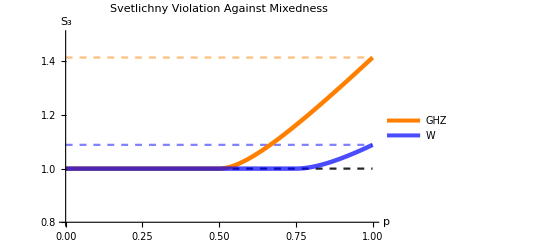

```mathematica
(*Compare GHZ and W violation against noise together*)
wviolation=ListLinePlot[wviolationvals,PlotRange->{{0,1},{0.9,Sqrt[2]}},PlotStyle->{Blue,Thickness[0.008],Opacity[0.7]},PlotLegends->{"W"}];
ghzviolation=ListLinePlot[ghzviolationvals,PlotStyle->{Orange,Thickness[0.008]},PlotLegends->{"GHZ"}];
boundary=ListLinePlot[{{0,1},{1,1}},
PlotStyle->{GrayLevel[0.15],Dashed},
PlotLabel->Style["Svetlichny Violation Against Mixedness",Black,20],
AxesLabel->{"  p","S_3"},
LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],AxesStyle->Directive[Black, 20,FontFamily->"Times New Roman"],
PlotRange->{All,{0.8,1.5}},Ticks->{Automatic,{0.8,0.9,{1.0,"1.0"},1.1,1.2,1.3,1.4}}];
maxw=ListLinePlot[{{0,1.0886621079036345},{1,1.0886621079036345}},PlotStyle->{Blue,Dashed,Opacity[0.5]}];
maxghz=ListLinePlot[{{0,Sqrt[2]},{1,Sqrt[2]}},PlotStyle->{Orange,Dashed,Opacity[0.5]}];
svetvsnoise=Show[boundary,maxw,maxghz,ghzviolation,wviolation]
```

```mathematica
Export[SystemDialogInput["FileSave", "ghz_w_svet.png"],svetvsnoise,Background->None];
```